# One-locus two-deme model of migration and selection with deme-independent dominance

## Life cycle

Random mating → viability selection → population regulation → migration

## Model and nomenclature

We consider a single locus with two alleles A_1 and A_2 and denote the frequencies of these two alleles in deme 1 and 2 by p_1 , q_1=1-p_1 and p_2, q_2=1-p_2, respectively. Each generation after population regulation and before random mating, a proportion m_ij of individuals in deme i is replaced by immigrants from deme j.

We denote the relative fitness of genotype A_k A_l in deme i by w_ikl and parameterise these fitnesses as follows:

w_111=1
w_112=w_121=1-h s_1
w_122=1-s_1

w_211=1-s_2
w_212=w_221=1-h s_2
w_222=1

The fitness parameterisation above is fully symmetrical with respect to the two demes and assumes that dominance is independent of the deme. Because relative fitnesses are bound to be positive, selection coefficients are constrained to be 0≤s_i≤1. Moreover, we assume that there is no underdominance nor overdominance, i.e. that 0≤h≤1. As a consequence, if s_i>0, then A_i confers a selective advantage in deme i and a disadvantage in deme j≠i. Note that h here reflects the dominance of the locally maladaptive allele, i.e. of A_i in deme j≠i.

Below, we also implement the parameterisation used by Sibly et al. (2021):

w_111=1
w_112=w_121=1+h s_1
w_122=1+s_1

w_211=1
w_212=w_221=1+h s_2
w_222=1+s_2

## Assumptions

Deterministic dynamics

Infinite population sizes

Deme-independent dominance

No underdominance nor overdominance

We assume no parental effect on the fitness of heterozygotes, i.e. w_kij=w_kji for i≠j.

## Generic functions

```mathematica
p[k_]:=If[k==1,p1,p2]
q[k_]:=1-p[k]
```

```mathematica
p[1]
```

p1

```mathematica
q[2]
```

1-p2

## Fitness functions and rules

### Relative fitness rules

```mathematica
wMat:={
{{w111,w112},{w121,w122}},
{{w211,w212},{w221,w222}}
}
```

```mathematica
w[k_,i_,j_]:=wMat⟦k,i,j⟧
```

```mathematica
fitRuleSymmet:={
w111 ->1,w112->1-h s1,w121->1-h s1,w122->1-s1,
w211 ->1-s2,w212->1-h s2,w221->1-h s2,w222->1
}

fitRuleSibly:={
w111 ->1,w112->1+h s1,w121->1+h s1,w122->1+s1,
w211 ->1,w212->1+h s2,w221->1+h s2,w222->1+s2
}
```

```mathematica
w[1,2,1]/.fitRuleSymmet
```

1-h s1

```mathematica
w[1,2,1]/.fitRuleSibly
```

1+h s1

### Marginal fitness function

```mathematica
w[k_,i_]:=If[i==1,
p[k]w[k,1,1]+q[k]w[k,1,2],
p[k]w[k,1,2]+q[k]w[k,2,2]
]
```

```mathematica
w[2,1]
```

p2 w211+(1-p2) w212

### Mean fitness function

```mathematica
w[k_]:=p[k]w[k,1]+q[k]w[k,2]
```

### Generic rules

```mathematica
qRule:={q1->1-p1,q2->1-p2}
```

## Migration rules

```mathematica
cRule:={c1->1+m21-m12,c2->1+m12-m21}
symmetMigRule:={m12->m,m21->m}
```

## Dynamical equations

### Recursion equations

Selection (Eq. 1)

```mathematica
p1Sel:=p1 w[1,1]/w[1]
p2Sel:=p2 w[2,1]/w[2]
```

```mathematica
p1SelSibly=p1Sel/.fitRuleSibly//Simplify
p2SelSibly=p2Sel/.fitRuleSibly//Simplify
```

(p1 (-1+h (-1+p1) s1))/(-1+(-1+p1) (1+(-1+2 h) p1) s1)

(p2 (-1+h (-1+p2) s2))/(-1+(-1+p2) (1+(-1+2 h) p2) s2)

```mathematica
p1SelSymmet=p1Sel/.fitRuleSymmet//Simplify
p2SelSymmet=p2Sel/.fitRuleSymmet//Simplify
```

(p1+h (-1+p1) p1 s1)/(1+(-1+p1) (1+(-1+2 h) p1) s1)

(p2 (1+h (-1+p2) s2-p2 s2))/(1+2 h (-1+p2) p2 s2-p2^2 s2)

As a check, we may use the symmetry of the model, noting that p_1=1-p_2:

```mathematica
p1SelSymmet-(1-(p2SelSymmet/.{p2->1-p2}/.{p2->p1}/.{s2->s1}))//FullSimplify
```

0

```mathematica
p1SelSiblyGiven:=(p1^2+(1+h s1)p1 q1)/(1+2h p1 q1 s1+s1 q1^2)
p2SelSiblyGiven:=(p2^2+(1+h s2)p2 q2)/(1+2h p2 q2 s2+s2 q2^2)
```

```mathematica
p1SelSibly-(p1SelSiblyGiven/.q1->(1-p1))//FullSimplify
p2SelSibly-(p2SelSiblyGiven/.q2->(1-p2))//FullSimplify
```

0

0

### Validation of Equations 2 to 5 of Sibly et al. (2021) Theor Popul Biol

Equation 2:

```mathematica
p1PrimePrime:=((1-m12)p1Prime+m21 p2Prime)/c1
p2PrimePrime:=((1-m21)p2Prime+m12 p1Prime)/c2
```

Assuming equilibrium, i.e. that p''_i=p_i, and solving for p'_1 yields Eq. (3).

```mathematica
p1PrimeEq3LRule=Solve[p1PrimePrime==p1,p1Prime]
```

{{p1Prime→(-c1 p1+m21 p2Prime)/(-1+m12)}}

```mathematica
p1PrimeEq3RRule=Solve[p2PrimePrime==p2,p1Prime]
```

{{p1Prime→(c2 p2-p2Prime+m21 p2Prime)/m12}}

Equating the two expressions for p'_1 and solving for p'_2 yields Eq. (4a).

```mathematica
K2Rule=Solve[(p1Prime/.p1PrimeEq3LRule)==(p1Prime/.p1PrimeEq3RRule),p2Prime]
```

{{p2Prime→(c1 m12 p1-c2 p2+c2 m12 p2)/(-1+m12+m21)}}

```mathematica
p2PrimeEq3LRule=Solve[p2PrimePrime==p2,p2Prime]
```

{{p2Prime→(m12 p1Prime-c2 p2)/(-1+m21)}}

```mathematica
p2PrimeEq3RRule=Solve[p1PrimePrime==p1,p2Prime]
```

{{p2Prime→(c1 p1-p1Prime+m12 p1Prime)/m21}}

Equating the two expressions for p'_2 and solving for p'_1 yields Eq. (4b).

```mathematica
K1Rule=Solve[(p2Prime/.p2PrimeEq3LRule)==(p2Prime/.p2PrimeEq3RRule),p1Prime]
```

{{p1Prime→(-c1 p1+c1 m21 p1+c2 m21 p2)/(-1+m12+m21)}}

Defining K_i according to Eq. (4):

```mathematica
K1=p1Prime/.K1Rule⟦1⟧
K2=p2Prime/.K2Rule⟦1⟧
```

(-c1 p1+c1 m21 p1+c2 m21 p2)/(-1+m12+m21)

(c1 m12 p1-c2 p2+c2 m12 p2)/(-1+m12+m21)

Above, we expressed the allele frequencies after selection and before migration in terms of allele frequencies after migration, assuming equilibrium. In Eq. 1 we already expressed allele frequencies after selection in terms of allele frequencies before selection. Next, we equate the two expressions for p'_i and solve for the selection coefficients.

#### Using the parameterisation of Sibly et al. (2021)

```mathematica
s1RuleSibly=Solve[κ1==p1SelSiblyGiven,s1]
```

{{s1→(p1^2+p1 q1-κ1)/(q1 (-h p1+2 h p1 κ1+q1 κ1))}}

```mathematica
p1^2+p1 q1-κ1/.q1->(1-p1)//FullSimplify
```

p1-κ1

```mathematica
s2RuleSibly=Solve[κ2==p2SelSiblyGiven,s2]
```

{{s2→(p2^2+p2 q2-κ2)/(q2 (-h p2+2 h p2 κ2+q2 κ2))}}

```mathematica
p2^2+p2 q2-κ2/.q2->(1-p2)//FullSimplify
```

p2-κ2

The same as above, but substituting q_i→(1-p_i):

```mathematica
s1RuleSiblyAlt=Solve[κ1==p1SelSiblyGiven/.q1->1-p1,s1]
```

{{s1→(-p1+κ1)/((-1+p1) (-h p1+κ1-p1 κ1+2 h p1 κ1))}}

```mathematica
s2RuleSiblyAlt=Solve[κ2==p2SelSiblyGiven/.q2->1-p2,s2]
```

{{s2→(-p2+κ2)/((-1+p2) (-h p2+κ2-p2 κ2+2 h p2 κ2))}}

#### Using the symmetrical parameterisation

```mathematica
s1RuleSymmet=Solve[κ1==p1SelSymmet,s1]
```

{{s1→(p1-κ1)/((-1+p1) (-h p1+κ1-p1 κ1+2 h p1 κ1))}}

```mathematica
s2RuleSymmet=Solve[κ2==p2SelSymmet,s2]
```

{{s2→(p2-κ2)/(p2 (h+p2-h p2-2 h κ2-p2 κ2+2 h p2 κ2))}}

```mathematica
(s1/.s1RuleSiblyAlt⟦1⟧)-(-s1/.s1RuleSymmet⟦1⟧)//FullSimplify
```

0

```mathematica
(s2/.s2RuleSiblyAlt⟦1⟧)-(-s2/.s2RuleSymmet⟦1⟧)//FullSimplify
```

-((p2-κ2) (p2^2+κ2-2 p2 κ2))/((-1+p2) p2 (p2-p2 κ2+h (-1+p2) (-1+2 κ2)) (κ2-p2 κ2+h p2 (-1+2 κ2)))

As expected based on the nature of the two parameterisations, s_1^(Sibly)=-s_1^(Symmet) , but the relationship between s_2^(Sibly) and s_2^(Symmet) is more complicated.

### Validation of Equations 6 and 7 of Sibly et al. (2021) Theor Popul Biol

#### Using the parameterisation of Sibly et al. (2021)

We follow Sibly et al. (2021) and compute the equilibrium frequencies of alleles given known selection coefficients.

Equating the two expressions for p'_1 and solving for p_1 yields Eq. (4a).

```mathematica
p1Rule=Solve[(p1Prime/.p1PrimeEq3LRule)==(p1Prime/.p1PrimeEq3RRule),p1]
```

{{p1→(c2 p2-c2 m12 p2-p2Prime+m12 p2Prime+m21 p2Prime)/(c1 m12)}}

Substituting from Eq. (1b) for p'_2 yields

```mathematica
p1SiblyRaw=p1/.p1Rule⟦1⟧/.{p2Prime->p2SelSiblyGiven}
```

(c2 p2-c2 m12 p2-(p2^2+p2 q2 (1+h s2))/(1+2 h p2 q2 s2+q2^2 s2)+(m12 (p2^2+p2 q2 (1+h s2)))/(1+2 h p2 q2 s2+q2^2 s2)+(m21 (p2^2+p2 q2 (1+h s2)))/(1+2 h p2 q2 s2+q2^2 s2))/(c1 m12)

```mathematica
p1SiblyGiven=(m12+m21-1)/(c1 m12)(p2(1+h s2 q2))/(1+2 h s2 p2 q2+s2 q2^2)+(1-m12)/(c1 m12)c2 p2
```

(c2 (1-m12) p2)/(c1 m12)+((-1+m12+m21) p2 (1+h q2 s2))/(c1 m12 (1+2 h p2 q2 s2+q2^2 s2))

```mathematica
(p1SiblyRaw-p1SiblyGiven)/.q2->(1-p2)//FullSimplify
```

0

```mathematica
p2Rule=Solve[(p2Prime/.p2PrimeEq3LRule)==(p2Prime/.p2PrimeEq3RRule),p2]
```

{{p2→(c1 p1-c1 m21 p1-p1Prime+m12 p1Prime+m21 p1Prime)/(c2 m21)}}

Substituting from Eq. (1b) for p'_2 yields

```mathematica
p2SiblyRaw=p2/.p2Rule⟦1⟧/.{p1Prime->p1SelSiblyGiven}
```

(c1 p1-c1 m21 p1-(p1^2+p1 q1 (1+h s1))/(1+2 h p1 q1 s1+q1^2 s1)+(m12 (p1^2+p1 q1 (1+h s1)))/(1+2 h p1 q1 s1+q1^2 s1)+(m21 (p1^2+p1 q1 (1+h s1)))/(1+2 h p1 q1 s1+q1^2 s1))/(c2 m21)

```mathematica
p2SiblyGiven=(m12+m21-1)/(c2 m21)(p1(1+h s1 q1))/(1+2 h s1 p1 q1+s1 q1^2)+(1-m21)/(c2 m21)c1 p1
```

(c1 (1-m21) p1)/(c2 m21)+((-1+m12+m21) p1 (1+h q1 s1))/(c2 m21 (1+2 h p1 q1 s1+q1^2 s1))

```mathematica
(p2SiblyRaw-p2SiblyGiven)/.q1->(1-p1)//FullSimplify
```

0

The steps above validate Eq. (7) in Sibly et al. (2021).

#### Using the symmetrical parameterisation

We follow Sibly et al. (2021) and compute the equilibrium frequencies of alleles given known selection coefficients.

Equating the two expressions for p'_1 and solving for p_1 yields Eq. (4a).

Substituting from Eq. (1b) for p'_2 yields

```mathematica
p1SymmetRaw=p1/.p1Rule⟦1⟧/.{p2Prime->p2SelSymmet}
```

(c2 p2-c2 m12 p2-(p2 (1+h (-1+p2) s2-p2 s2))/(1+2 h (-1+p2) p2 s2-p2^2 s2)+(m12 p2 (1+h (-1+p2) s2-p2 s2))/(1+2 h (-1+p2) p2 s2-p2^2 s2)+(m21 p2 (1+h (-1+p2) s2-p2 s2))/(1+2 h (-1+p2) p2 s2-p2^2 s2))/(c1 m12)

```mathematica
p1Symmet=(m12+m21-1)/(c1 m12)(p2-p2^2 s2-h p2 q2 s2)/(1-2 h p2 q2 s2-p2^2 s2)+(1-m12)/(c1 m12)c2 p2
```

(c2 (1-m12) p2)/(c1 m12)+((-1+m12+m21) (p2-p2^2 s2-h p2 q2 s2))/(c1 m12 (1-p2^2 s2-2 h p2 q2 s2))

```mathematica
(p1SymmetRaw-p1Symmet)/.q2->(1-p2)//FullSimplify
```

0

Substituting from Eq. (1b) for p'_2 yields

```mathematica
p2SymmetRaw=p2/.p2Rule⟦1⟧/.{p1Prime->p1SelSymmet}
```

(c1 p1-c1 m21 p1-(p1+h (-1+p1) p1 s1)/(1+(-1+p1) (1+(-1+2 h) p1) s1)+(m12 (p1+h (-1+p1) p1 s1))/(1+(-1+p1) (1+(-1+2 h) p1) s1)+(m21 (p1+h (-1+p1) p1 s1))/(1+(-1+p1) (1+(-1+2 h) p1) s1))/(c2 m21)

```mathematica
p2Symmet=(m12+m21-1)/(c2 m21)(p1-h p1 q1 s1)/(1-2 h p1 q1 s1-q1^2 s1)+(1-m21)/(c2 m21)c1 p1
```

(c1 (1-m21) p1)/(c2 m21)+((-1+m12+m21) (p1-h p1 q1 s1))/(c2 m21 (1-2 h p1 q1 s1-q1^2 s1))

```mathematica
(p2SymmetRaw-p2Symmet)/.q1->(1-p1)//FullSimplify
```

0

## Numerical solution for equilibrium allele frequencies

### Remark

There are multiple types of equilibria. Two trivial equilibria correspond to the global loss ((p̂)_1=(p̂)_2=0) and fixation ((p̂)_1=(p̂)_2=1) of the focal allele A_1. Two further, marginal, equilibria correspond to the case where A_1 is fixed in one and lost in the other deme ((p̂)_1=1,(p̂)_2=0; (p̂)_1=0,(p̂)_2=1). Last, there may be an equilibrium at which A_1is polymorphic in both demes (0<(p̂)_1,(p̂)_2<1).

### Using parameterisation by Sibly et al. (2021)

From Eq. (7) of Sibly et al. (2021):

```mathematica
EqPSibly1:=p1==(m12+m21-1)/(c1 m12)(p2(1+h s2 q2))/(1+2 h s2 p2 q2+s2 q2^2)+(1-m12)/(c1 m12)c2 p2
EqPSibly2:=p2==(m12+m21-1)/(c2 m21)(p1(1+h s1 q1))/(1+2 h s1 p1 q1+s1 q1^2)+(1-m21)/(c2 m21)c1 p1
```

Specific test values of the parameters, as per Fig. 2 of Sibly et al. (2021):

```mathematica
mTest1:=0.05
s1Test1:=-0.01
s1Test1Alt:=0.01
s2Test1:=0.01
hTest1:=1.
hTest1Alt:=0.
```

```mathematica
{EqPSibly1,EqPSibly2,0<=p1<=1,0<=p2<=1}/.qRule/.cRule/.symmetMigRule
```

{p1==((1-m) p2)/m+((-1+2 m) p2 (1+h (1-p2) s2))/(m (1+(1-p2)^2 s2+2 h (1-p2) p2 s2)),p2==((1-m) p1)/m+((-1+2 m) p1 (1+h (1-p1) s1))/(m (1+(1-p1)^2 s1+2 h (1-p1) p1 s1)),0≤p1≤1,0≤p2≤1}

```mathematica
NSolveSibly[m_,s1_,s2_,h_]:=NSolve[
{p1==((1-m) p2)/m+((-1+2 m) p2 (1+h (1-p2) s2))/(m (1+(1-p2)^2 s2+2 h (1-p2) p2 s2)),p2==((1-m) p1)/m+((-1+2 m) p1 (1+h (1-p1) s1))/(m (1+(1-p1)^2 s1+2 h (1-p1) p1 s1)),0≤p1≤1,0≤p2≤1},{p1,p2},
Reals
]
```

```mathematica
NSolveSibly[mTest1,s1Test1,s2Test1,hTest1]
```

{{p1→0.707456,p2→0.680969},{p1→7.37089×10^-10,p2→7.37089×10^-10},{p1→0.,p2→0.}}

```mathematica
Manipulate[
NSolveSibly[m,s1,s2,h]//Chop,
{{m,mTest1},0,1},{{s1,s1Test1},-1.,100},{{s2,s2Test1},-1.,100},{{h,hTest1},0,1}
]
```

With the parameter values used by Sibly et al. (2021) in their Fig. 2 (h=1,m=0.05,s_1=-0.01,s_2=0.01), the internal equilibrium is given by the first pair of coordinates in the output above. We store these values for reference in a plot below:

```mathematica
pEqValSiblyFig2=NSolveSibly[mTest1,s1Test1,s2Test1,hTest1]⟦1⟧
```

{p1→0.707456,p2→0.680969}

### Using symmetrical parameterisation

```mathematica
EqPSymmet1:=p1==(m12+m21-1)/(c1 m12)(p2-p2^2 s2-h p2 q2 s2)/(1-2 h p2 q2 s2-p2^2 s2)+(1-m12)/(c1 m12)c2 p2
EqPSymmet2:=p2==(m12+m21-1)/(c2 m21)(p1-h p1 q1 s1)/(1-2 h p1 q1 s1-q1^2 s1)+(1-m21)/(c2 m21)c1 p1
```

```mathematica
{EqPSymmet1,EqPSymmet2,0<=p1<=1,0<=p2<=1}/.qRule/.cRule/.symmetMigRule
```

{p1==((1-m) p2)/m+((-1+2 m) (p2-h (1-p2) p2 s2-p2^2 s2))/(m (1-2 h (1-p2) p2 s2-p2^2 s2)),p2==((1-m) p1)/m+((-1+2 m) (p1-h (1-p1) p1 s1))/(m (1-(1-p1)^2 s1-2 h (1-p1) p1 s1)),0≤p1≤1,0≤p2≤1}

```mathematica
NSolveSymmet[m_,s1_,s2_,h_]:=NSolve[
{p1==((1-m) p2)/m+((-1+2 m) (p2-h (1-p2) p2 s2-p2^2 s2))/(m (1-2 h (1-p2) p2 s2-p2^2 s2)),p2==((1-m) p1)/m+((-1+2 m) (p1-h (1-p1) p1 s1))/(m (1-(1-p1)^2 s1-2 h (1-p1) p1 s1)),0≤p1≤1,0≤p2≤1},{p1,p2},
Reals
]
```

```mathematica
NSolveSymmet[mTest1,s1Test1Alt,s2Test1,hTest1Alt]
```

{{p1→1.,p2→1.},{p1→0.511023,p2→0.488977},{p1→0.,p2→0.}}

```mathematica
Manipulate[
NSolveSymmet[m,s1,s2,h]//Chop,
{{m,mTest1},0,1},{{s1,s1Test1Alt},0.,1.},{{s2,s2Test1},0.,1.},{{h,hTest1Alt},0,1}
]
```

```mathematica
pEqValSymmet=NSolveSymmet[mTest1,s1Test1Alt,s2Test1,hTest1Alt]⟦2⟧
```

{p1→0.511023,p2→0.488977}

## Recursion equations for migration and selection

### Parameterisation by Sibly et al. (2021)

```mathematica
p1PrimePrime
```

((1-m12) p1Prime+m21 p2Prime)/c1

```mathematica
p2PrimePrime
```

(m12 p1Prime+(1-m21) p2Prime)/c2

```mathematica
p1SelSibly
```

(p1 (-1+h (-1+p1) s1))/(-1+(-1+p1) (1+(-1+2 h) p1) s1)

```mathematica
p2SelSibly
```

(p2 (-1+h (-1+p2) s2))/(-1+(-1+p2) (1+(-1+2 h) p2) s2)

```mathematica
p1PrimePrime/.{p1Prime->p1SelSibly,p2Prime->p2SelSibly}/.cRule/.qRule//Simplify
p2PrimePrime/.{p1Prime->p1SelSibly,p2Prime->p2SelSibly}/.cRule/.qRule//Simplify
```

(((1-m12) p1 (-1+h (-1+p1) s1))/(-1+(-1+p1) (1+(-1+2 h) p1) s1)+(m21 p2 (-1+h (-1+p2) s2))/(-1+(-1+p2) (1+(-1+2 h) p2) s2))/(1-m12+m21)

((m12 p1 (-1+h (-1+p1) s1))/(-1+(-1+p1) (1+(-1+2 h) p1) s1)+((1-m21) p2 (-1+h (-1+p2) s2))/(-1+(-1+p2) (1+(-1+2 h) p2) s2))/(1+m12-m21)

Initial allele frequencies as per Sibly et al. (“initial frequency of Q of 0.01”, which translates to p_1=p_2=0.99):

```mathematica
p1Init1:=0.99
p2Init1:=0.99
```

```mathematica
Remove[p1RecSibly,p2RecSibly]
p1RecSibly[m12_,m21_,s1_,s2_,h_,0]:=p1Init1
p2RecSibly[m12_,m21_,s1_,s2_,h_,0]:=p2Init1

p1RecSibly[m12_,m21_,s1_,s2_,h_,t_]:=p1RecSibly[m12,m21,s1,s2,h,t]=1/(1-m12+m21)(((1-m12) p1RecSibly[m12,m21,s1,s2,h,t-1] (-1+h (-1+p1RecSibly[m12,m21,s1,s2,h,t-1]) s1))/(-1+(-1+p1RecSibly[m12,m21,s1,s2,h,t-1]) (1+(-1+2 h) p1RecSibly[m12,m21,s1,s2,h,t-1]) s1)+(m21 p2RecSibly[m12,m21,s1,s2,h,t-1] (-1+h (-1+p2RecSibly[m12,m21,s1,s2,h,t-1]) s2))/(-1+(-1+p2RecSibly[m12,m21,s1,s2,h,t-1]) (1+(-1+2 h) p2RecSibly[m12,m21,s1,s2,h,t-1]) s2))
p2RecSibly[m12_,m21_,s1_,s2_,h_,t_]:=p2RecSibly[m12,m21,s1,s2,h,t]=1/(1+m12-m21)((m12 p1RecSibly[m12,m21,s1,s2,h,t-1] (-1+h (-1+p1RecSibly[m12,m21,s1,s2,h,t-1]) s1))/(-1+(-1+p1RecSibly[m12,m21,s1,s2,h,t-1]) (1+(-1+2 h) p1RecSibly[m12,m21,s1,s2,h,t-1]) s1)+((1-m21) p2RecSibly[m12,m21,s1,s2,h,t-1] (-1+h (-1+p2RecSibly[m12,m21,s1,s2,h,t-1]) s2))/(-1+(-1+p2RecSibly[m12,m21,s1,s2,h,t-1]) (1+(-1+2 h) p2RecSibly[m12,m21,s1,s2,h,t-1]) s2))
```

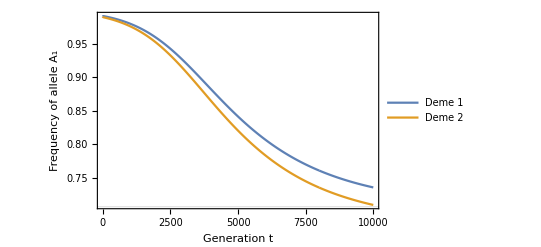

```mathematica
DiscretePlot[
{
p1RecSibly[mTest1,mTest1,s1Test1,s2Test1,hTest1,t],p2RecSibly[mTest1,mTest1,s1Test1,s2Test1,hTest1,t]
},
{t,0,10000},
GridLines->{None,{p1,p2}/.pEqValSiblyFig2},
PlotRange->{Full,Full},
Filling->None,
Joined->True,
Frame->True,
FrameLabel->{"Generation t","Frequency of allele A_1"},
PlotLegends->{"Deme 1","Deme 2"}
]
```

The plot above should correspond to Fig. 3 in Sibly et al. (2021), but it does not.

The same plot as above, but extending the x axis to 50,000 generations to see if the equilibrium allele frequencies as determined by numerical solution are reached:

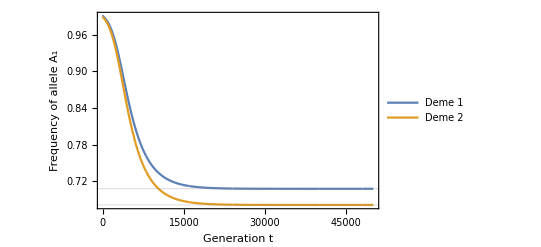

```mathematica
DiscretePlot[
{
p1RecSibly[mTest1,mTest1,s1Test1,s2Test1,hTest1,t],p2RecSibly[mTest1,mTest1,s1Test1,s2Test1,hTest1,t]
},
{t,0,50000},
GridLines->{None,{p1,p2}/.pEqValSiblyFig2},
PlotRange->{Full,Full},
Filling->None,
Joined->True,
Frame->True,
FrameLabel->{"Generation t","Frequency of allele A_1"},
PlotLegends->{"Deme 1","Deme 2"}
]
```

Figure 2 in Sibly et al. (2021) seems to illustrate the dynamics for another parameter combination than the one reported, i.e. not for m=0.05,s_1=-0.01,s_2=0.01,h=1.0. Alternatively, the might be an error in the implementation of the simulations by Sibly et al. (2020).

### Symmetrical parameterisation

```mathematica
p1PrimePrime
```

((1-m12) p1Prime+m21 p2Prime)/c1

```mathematica
p2PrimePrime
```

(m12 p1Prime+(1-m21) p2Prime)/c2

```mathematica
p1SelSymmet
```

(p1+h (-1+p1) p1 s1)/(1+(-1+p1) (1+(-1+2 h) p1) s1)

```mathematica
p2SelSymmet
```

(p2 (1+h (-1+p2) s2-p2 s2))/(1+2 h (-1+p2) p2 s2-p2^2 s2)

```mathematica
(1-(p2SelSymmet/.{p2->1-p2}/.{p2->p1,s2->s1}))-p1SelSymmet//FullSimplify
```

0

```mathematica
qRule
```

{q1→1-p1,q2→1-p2}

```mathematica
p1SelMigSymmet=p1PrimePrime/.{p1Prime->p1SelSymmet,p2Prime->p2SelSymmet}/.cRule//Simplify
p2SelMigSymmet=p2PrimePrime/.{p1Prime->p1SelSymmet,p2Prime->p2SelSymmet}/.cRule//Simplify
```

(((1-m12) (p1+h (-1+p1) p1 s1))/(1+(-1+p1) (1+(-1+2 h) p1) s1)+(m21 p2 (1+h (-1+p2) s2-p2 s2))/(1+2 h (-1+p2) p2 s2-p2^2 s2))/(1-m12+m21)

((m12 (p1+h (-1+p1) p1 s1))/(1+(-1+p1) (1+(-1+2 h) p1) s1)+((1-m21) p2 (1+h (-1+p2) s2-p2 s2))/(1+2 h (-1+p2) p2 s2-p2^2 s2))/(1+m12-m21)

Initial allele frequencies as per Sibly et al. (“initial frequency of Q of 0.01”, which translates to p_1=p_2=0.99), as above.

```mathematica
p1Init1:=0.99
p2Init1:=0.99
```

```mathematica
Remove[p1RecSymmet,p2RecSymmet]
p1RecSymmet[m12_,m21_,s1_,s2_,h_,0]:=p1Init1
p2RecSymmet[m12_,m21_,s1_,s2_,h_,0]:=p2Init1

p1RecSymmet[m12_,m21_,s1_,s2_,h_,t_]:=p1RecSymmet[m12,m21,s1,s2,h,t]=1/(1-m12+m21)(((1-m12) (p1RecSymmet[m12,m21,s1,s2,h,t-1]+h (-1+p1RecSymmet[m12,m21,s1,s2,h,t-1]) p1RecSymmet[m12,m21,s1,s2,h,t-1] s1))/(1+(-1+p1RecSymmet[m12,m21,s1,s2,h,t-1]) (1+(-1+2 h) p1RecSymmet[m12,m21,s1,s2,h,t-1]) s1)+(1/(1+2 h (-1+p2RecSymmet[m12,m21,s1,s2,h,t-1]) p2RecSymmet[m12,m21,s1,s2,h,t-1] s2-p2RecSymmet[m12,m21,s1,s2,h,t-1]^2 s2))m21 p2RecSymmet[m12,m21,s1,s2,h,t-1] (1+h (-1+p2RecSymmet[m12,m21,s1,s2,h,t-1]) s2-p2RecSymmet[m12,m21,s1,s2,h,t-1] s2))
p2RecSymmet[m12_,m21_,s1_,s2_,h_,t_]:=p2RecSymmet[m12,m21,s1,s2,h,t]=1/(1+m12-m21)((m12 (p1RecSymmet[m12,m21,s1,s2,h,t-1]+h (-1+p1RecSymmet[m12,m21,s1,s2,h,t-1]) p1RecSymmet[m12,m21,s1,s2,h,t-1] s1))/(1+(-1+p1RecSymmet[m12,m21,s1,s2,h,t-1]) (1+(-1+2 h) p1RecSymmet[m12,m21,s1,s2,h,t-1]) s1)+(1/(1+2 h (-1+p2RecSymmet[m12,m21,s1,s2,h,t-1]) p2RecSymmet[m12,m21,s1,s2,h,t-1] s2-p2RecSymmet[m12,m21,s1,s2,h,t-1]^2 s2))(1-m21) p2RecSymmet[m12,m21,s1,s2,h,t-1] (1+h (-1+p2RecSymmet[m12,m21,s1,s2,h,t-1]) s2-p2RecSymmet[m12,m21,s1,s2,h,t-1] s2))
```

```mathematica
mTest1:=0.05
s1Test1:=-0.01
s1Test1Alt:=0.01
s2Test1:=0.01
hTest1:=1.
hTest1Alt:=0.
```

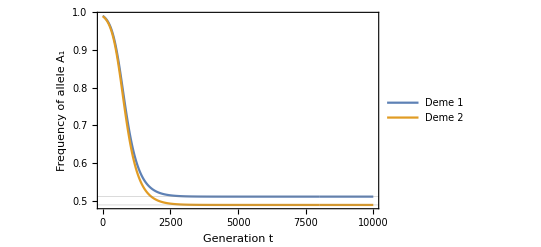

```mathematica
DiscretePlot[
{
p1RecSymmet[mTest1,mTest1,s1Test1Alt,s2Test1,hTest1Alt,t],p2RecSymmet[mTest1,mTest1,s1Test1Alt,s2Test1,hTest1Alt,t]
},
{t,0,10000},
GridLines->{None,{p1,p2}/.pEqValSymmet},
PlotRange->{Full,Full},
Filling->None,
Joined->True,
Frame->True,
FrameLabel->{"Generation t","Frequency of allele A_1"},
PlotLegends->{"Deme 1","Deme 2"}
]
```

The same plot as above, but extending the x axis to 50,000 generations to see if the equilibrium allele frequencies as determined by numerical solution are reached:

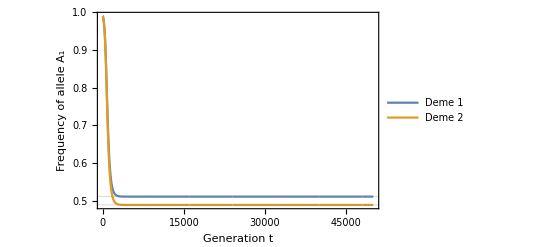

```mathematica
DiscretePlot[
{
p1RecSymmet[mTest1,mTest1,s1Test1Alt,s2Test1,hTest1Alt,t],p2RecSymmet[mTest1,mTest1,s1Test1Alt,s2Test1,hTest1Alt,t]
},
{t,0,50000},
GridLines->{None,{p1,p2}/.pEqValSymmet},
PlotRange->{Full,Full},
Filling->None,
Joined->True,
Frame->True,
FrameLabel->{"Generation t","Frequency of allele A_1"},
PlotLegends->{"Deme 1","Deme 2"}
]
```

## Not used

### Formulae for F_ST

FstSibly=(pT(1-pT)-1/2 p1(1-p1)-1/2 p2(1-p2))/(pT(1-pT))/.{pT->(p1SiblyGiven+p2SiblyGiven),p1->p1SiblyGiven,p2->p2SiblyGiven}/.{q1->1-p1,q2->1-p2}//Simplify

$Aborted

FstSymmet=(pT(1-pT)-1/2 p1(1-p1)-1/2 p2(1-p2))/(pT(1-pT))/.{pT->(p1Symmet+p2Symmet),p1->p1Symmet,p2->p2Symmet}/.{q1->1-p1,q2->1-p2}//Simplify

(-((-c1 (-1+m21) p1+((-1+m12+m21) (p1+h (-1+p1) p1 s1))/(1+(-1+p1) (1+(-1+2 h) p1) s1)) (1+(c1 (-1+m21) p1)/(c2 m21)-((-1+m12+m21) (p1+h (-1+p1) p1 s1))/(c2 m21 (1+(-1+p1) (1+(-1+2 h) p1) s1))))/(2 c2 m21)+(1+(c1 (-1+m21) p1)/(c2 m21)+(c2 (-1+m12) p2)/(c1 m12)-((-1+m12+m21) (p1+h (-1+p1) p1 s1))/(c2 m21 (1+(-1+p1) (1+(-1+2 h) p1) s1))-((-1+m12+m21) p2 (1+h (-1+p2) s2-p2 s2))/(c1 m12 (1+2 h (-1+p2) p2 s2-p2^2 s2))) (-(c1 (-1+m21) p1)/(c2 m21)-(c2 (-1+m12) p2)/(c1 m12)+((-1+m12+m21) (p1+h (-1+p1) p1 s1))/(c2 m21 (1+(-1+p1) (1+(-1+2 h) p1) s1))+((-1+m12+m21) p2 (1+h (-1+p2) s2-p2 s2))/(c1 m12 (1+2 h (-1+p2) p2 s2-p2^2 s2)))+(p2 (-((-1+m12+m21) (1+h (-1+p2) s2-p2 s2))+c2 (-1+m12) (1+2 h (-1+p2) p2 s2-p2^2 s2)) (c1 m12 (1+2 h (-1+p2) p2 s2-p2^2 s2)+p2 (-((-1+m12+m21) (1+h (-1+p2) s2-p2 s2))+c2 (-1+m12) (1+2 h (-1+p2) p2 s2-p2^2 s2))))/(2 c1^2 m12^2 (1+2 h (-1+p2) p2 s2-p2^2 s2)^2))/((1+(c1 (-1+m21) p1)/(c2 m21)+(c2 (-1+m12) p2)/(c1 m12)-((-1+m12+m21) (p1+h (-1+p1) p1 s1))/(c2 m21 (1+(-1+p1) (1+(-1+2 h) p1) s1))-((-1+m12+m21) p2 (1+h (-1+p2) s2-p2 s2))/(c1 m12 (1+2 h (-1+p2) p2 s2-p2^2 s2))) (-(c1 (-1+m21) p1)/(c2 m21)-(c2 (-1+m12) p2)/(c1 m12)+((-1+m12+m21) (p1+h (-1+p1) p1 s1))/(c2 m21 (1+(-1+p1) (1+(-1+2 h) p1) s1))+((-1+m12+m21) p2 (1+h (-1+p2) s2-p2 s2))/(c1 m12 (1+2 h (-1+p2) p2 s2-p2^2 s2))))